# Project 1 - IX1501

## A project by William Lewin & Elias Chahine

wlewin@kth.se & echahine@kth.se

## Summary

In the discrete math course you learned how to do a census by computing all possibilities and use the classical definition of probability. In the following problems you are expected to use convolution.
-Graphics-
At a dice game you throw five dice in the form of the Platonic solids. The dice are numbered with integers 1,2,…,n where n is the number of sides. The tetrahedron has its result number (1-4) written at the vertex pointing up. All other bodies have the result number on the side facing up. 

At a fun-fair stall you can win a giant Teddy bear if you participate in the mentioned dice game. You invest €2 and then throw the five dice. If the sum S satisfies S≤10 or S≥45 you will win the Teddy.

Determine the exact probability function of the sum.

Determine the exact probability of winning the Teddy prize. Also give a floating point answer.

Determine the expected investment to win a Teddy.

What’s the probability of winning (at least one) Teddy if you play twenty times?

## Mathematic formulas & equations

### Determine the exact probability function of the sum.

### Determine the exact probability of winning the Teddy prize. Also give a floating point answer.

### Determine the expected investment to win a Teddy.

### What’s the probability of winning (at least one) Teddy if you play twenty times?

## Discussion

## Code

```mathematica
ClearAll["Global`*"]
pyramid = PolyhedronData["TriangularPyramid","FaceCount"]
cube = PolyhedronData["Cube","FaceCount"]
octahedron = PolyhedronData["Octahedron","FaceCount"]
dodecahedron = PolyhedronData["Dodecahedron","FaceCount"]
icosahedron = PolyhedronData["Icosahedron","FaceCount"]




(*Random throws*)
d1 := RandomInteger[{1,pyramid}]
d2 := RandomInteger[{1,cube}]
d3 := RandomInteger[{1,octahedron}]
d4 := RandomInteger[{1,dodecahedron}]
d5 := RandomInteger[{1,icosahedron}]
```

4

6

8

12

20

```mathematica
(*Prob. P1 ≤ 10 och P2 ≥ 45
convolutePyramidCube
convolutePCOctagon
convolutePCODodecahedron
convolutePCODIco....
*)
ClearAll["`*"]
pyramidfX[k_]=Piecewise[{{1/4,1≤k≤4}}];
cubefX[k_]=Piecewise[{{1/6,1≤k≤6}}];
octafX[k_]:=Piecewise[{{1/8,1≤k≤8}}];
dodefX[k_]:=Piecewise[{{1/12,1≤k≤12}}];
icofX[k_]:=Piecewise[{{1/20,1≤k≤20}}];
Plot[{pyramidfX[k],cubefX[k],octafX[k],dodefX[k],icofX[k]},{k,0,20}];
(*S = X + Y + Z ....*)
```

```mathematica
convolutePyramidCube[k_]=DiscreteConvolve[pyramidfX[x],cubefX[x],x,k];
convolutePCOctagon[k_]=DiscreteConvolve[convolutePyramidCube[x],octafX[x],x,k];
convolutePCODodecahedron[k_]= DiscreteConvolve[convolutePCOctagon[x],dodefX[x],x,k];
convolutePCODIcosahedron[k_]=DiscreteConvolve[convolutePCODodecahedron[x],icofX[x],x,k];
convPCODI[x]=convolutePCODIcosahedron[x];(*One big piecewise function*)
```

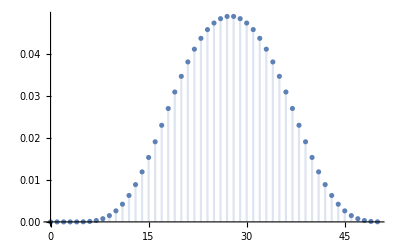

```mathematica
DiscretePlot[convolutePCODIcosahedron[x],{x,0,50}]
```

```mathematica
convPCODI[x]
```

Piecewise[{{1/46080, x==5||x==50}, {1/9216, x==6||x==49}, {1/3072, x==7||x==48}, {7/9216, x==8||x==47}, {23/15360, x==9||x==46}, {121/46080, x==10||x==45}, {97/23040, x==11||x==44}, {29/4608, x==12||x==43}, {409/46080, x==13||x==42}, {61/5120, x==14||x==41}, {707/46080, x==15||x==40}, {293/15360, x==16||x==39}, {53/2304, x==17||x==38}, {311/11520, x==18||x==37}, {95/3072, x==19||x==36}, {1597/46080, x==20||x==35}, {39/1024, x==21||x==34}, {379/9216, x==22||x==33}, {1007/23040, x==23||x==32}, {211/4608, x==24||x==31}, {1091/23040, x==25||x==30}, {223/4608, x==26||x==29}, {1127/23040, 26<x<29}, {0, True}}]